## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
```

## Equation and and Eigenvalue function

```mathematica
<<"Definitions/Teukolsky.wl"
<<"Definitions/SWSH.wl"
```

```mathematica
Eq=EqRadial/.RuleKRadial;
```

```mathematica
Clear@ℰ;
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real?Negative]:=ℰ[𝓈,ℓ,-𝓂,-𝒸];
ℰ[𝓈_Integer?Negative,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]:=ℰ[-𝓈,ℓ,𝓂,𝒸];
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]:=ℰ[𝓈,ℓ,𝓂][𝒸];
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer]/;(ℓ≥Max[Abs[𝓈],Abs[𝓂]]):=ℰ[𝓈,ℓ,𝓂]=Interpolation[Import@GetSWSHEigenFile[𝓈,ℓ,𝓂]]
```

## Parameter rules and equation simplification

```mathematica
RuleR={R->Function[x,rp^-s x^(-s-I χ/τ)f[x]]};
nCoef=8;
RuleF={f->Function[x,∑_(n=0)^nCoef 𝒶[n] x^n]};
RuleBoundaryBHole={𝒶[0]->1,𝒷[0]->(-ℬ τ^2)/(4 (ⅈ τ/2+χ) χ)};
EquationF=PowerExpand@Simplify[x^(s+I χ/τ)x (x+τ) (Eq/.RuleR)];
RuleParams={τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),ℬ->Sqrt[(λ+s(s+1))^2-4((𝒥 ω̄)/rp)^2+4m (𝒥 ω̄)/rp],  
λ->((𝒥 ω̄)/rp)^2-2m((𝒥 ω̄)/rp)+𝔈-s(s+1)};
RuleEigenParamCoef={𝔈->(EigenCoef/.Ruleκpm).Table[((𝒥 ω̄)/rp)^(n-1),{n,Length@EigenCoef}]+s(s+1)};
RuleEigenParamLeaver={𝔈->EigenLeaver[s,l,m,(𝒥 ω̄)/rp]};
RuleEigenParam={𝔈->ℰ[s,l,m,(𝒥 ω̄)/rp]};
RuleAllParams=RuleParams~Join~RuleEigenParam;
```

```mathematica
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_]:=PowerExpand[(#1/.RuleBoundaryBHole)//.RuleAllParams/.{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿}]&;
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_,𝓌_]:=PowerExpand[(#1/.RuleBoundaryBHole)//.RuleAllParams/.{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿,ω̄->𝓌}]&;
```

```mathematica
FSeriesCoef=Chop@First@Solve[CoefficientList[EquationF/.RuleF,x][[2;;nCoef+1]]==0,Table[𝒶[n],{n,1,nCoef}]//Evaluate];
```

## Equation solver definition

```mathematica
x0=10^-14.;
xM:=(2 π)/Abs[ω̄]*750;
```

```mathematica
ClearAll@SolveωF;
IncreasePrecision={PrecisionGoal->12,AccuracyGoal->15,MaxSteps->Automatic};
SolveωF[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ]:=SolveωF[𝒿,𝓈,ℓ,𝓂,Range[0.0001,0.65,0.004]]
SolveωF[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,{omega__?NumberQ},opts:OptionsPattern[]]/;0<𝒿<1&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Block[{eqF,delω,ics,fInf,k=0,last,olist},
SetSharedVariable[k];
ParallelEvaluate[last=AbsoluteTime[];localk=1];
{eqF,delω,ics,fInf}=ReplaceParams[𝒿,𝓈,ℓ,𝓂][{EquationF,m Ω̄,({f[x0],f'[x0]}/.RuleF/.FSeriesCoef)/.If[𝓈<0,{𝒶->𝒷},{}],f[xM] ⅇ^(ⅈ(𝓈 ω̄ xM-χ/τ Log[xM]))}];
olist=DeleteCases[{omega},delω];
Monitor[ParallelTable[localk++;
If[AbsoluteTime[]-last>1,
last=AbsoluteTime[];k+=localk;localk=0];{𝒿,ω̄,fInf}/.First@NDSolve[{eqF==0,{f[x0],f'[x0]}==ics},f,{x,x0,xM},Sequence@@FilterRules[{opts}, Options[NDSolve]]],{ω̄,olist}],
ProgressIndicator[k,{0,Length@olist}]]
];
```

## Export data

```mathematica
Clear[FormatZ,Formatϕ]
FormatZ[ℓ_,𝓂_]:=({#1,#2,-(ω̄ τ^2 Abs[𝒶[0]]^2)/(χ Abs[#3]^2),-1/(1+(χ Abs[#4]^2)/(τ^2 ω̄ Abs[𝒶[0]]^2)),Abs[#4/#3]^2-1}//ReplaceParams[#1,-1,ℓ,𝓂,#2])&;
Formatϕ[ℓ_,𝓂_]:={#1,#2,Re@#3,Im@#3,Re@#4,Im@#4}&;
```

```mathematica
Spin=Range[0.01,0.99,0.01]∪{0.995,0.999,0.9995,0.9999};
```

```mathematica
Omega=Function[𝒿,0.0001+Range@@{0,Round[(1+√(1-𝒿^2)) 0.6,0.05],Round[1/450 Round[(1+√(1-𝒿^2)) 0.6,0.05],0.0005]}];
OmegaDetailed=Function[𝒿,0.0001+Range@@{0,First@TakeSmallest[{𝒿,Round[(1+√(1-𝒿^2)) 0.6,0.05]},1],First@TakeSmallest[{Ceiling[0.01𝒿,0.0001],Round[1/450 Round[(1+√(1-𝒿^2)) 0.6,0.05],0.0005]},1]}];
```

```mathematica
Clear[PutAppendCSV,ExportAllCSV];
PutAppendCSV[file_,data_?ArrayQ]:=WriteString[file,ExportString[data,"CSV"],"\n"];
ExportAllCSV[𝒿:{__?NumberQ}|𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,OmegaF_Function,eof_String:"",opts:OptionsPattern[]]/;And@@Thread[0<𝒿<1]&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=Block[{dataP,dataM,tmpPrint,spins= Flatten[{𝒿}],Ns,spin,time,timeList,fileZ,fileϕ},
Ns=Length@spins;
fileZ=GetZFile[Abs@𝓈,ℓ,𝓂,eof];
fileϕ=GetϕFile[Abs@𝓈,ℓ,𝓂,eof];
Quiet@DeleteFile[{fileZ,fileϕ}];
time=First@AbsoluteTiming@Do[
tmpPrint=PrintTemporary@StringRiffle[{"𝓈 = +",Abs@𝓈,", 𝒥 = ",spins⟦i⟧,"  (",2i-1," of ",2Ns,")"},""];
dataP=SolveωF[spins⟦i⟧,Abs@𝓈,ℓ,𝓂,OmegaF@spins⟦i⟧,opts]; 
NotebookDelete[tmpPrint];
tmpPrint=PrintTemporary@StringRiffle[{"𝓈 = ",-Abs[𝓈],", 𝒥 = ",spins⟦i⟧,"  (",2 i," of ",2 Ns,")"},""];
dataM=SolveωF[spins⟦i⟧,-Abs@𝓈,ℓ,𝓂,OmegaF@spins⟦i⟧,opts];
PutAppendCSV[fileZ,FormatZ[ℓ,𝓂]@@@Flatten[{dataP,dataM},{{2},{1,3}}]⟦All,{1,2,3,6}⟧];
PutAppendCSV[fileϕ,Formatϕ[ℓ,𝓂]@@@Flatten[{dataP,dataM},{{2},{1,3}}]⟦All,{1,2,3,6}⟧];
NotebookDelete[tmpPrint];
,{i,Ns}];
Quiet@*Close/@{fileZ,fileϕ};
timeList=First@QuantityMagnitude@UnitConvert[Quantity[Round@time,"Seconds"],MixedUnit[{"Hours","Minutes","Seconds"}]];
Print[StringRiffle[{"Completed",eof,"files with (𝓈,ℓ,m)="}]<>StringRiffle[{Abs@𝓈,ℓ,𝓂},{"(",",",")"}]<>StringRiffle[{" for",Ns,"spin(s)"}]<>StringJoin@@Riffle[{" in ","h ","m ","s"},ToString/@MapAt[IntegerString[#,10,2]&,timeList,{{2},{3}}]]];
]
```

```mathematica
(*ExportAllCSV[0.99,1,1,1,Omega,"test2"]*)
```

```mathematica
(*ExportAllCSV[1,1,1,{0.995,0.999,0.9995,0.9999},Omega,"precision",IncreasePrecision]*)
```

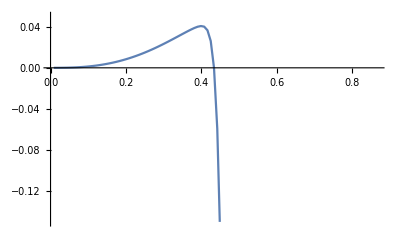

```mathematica
Import@GetZFileBCP[-1,1,1]//GroupBy[#,First-> Rest]&//Last//ListPlot[#,PlotRange->{-0.15,0.05},Joined->True]&
```

## Calculate in/out

```mathematica
InWavePackets={{0.99,1,1,0.4891,1.0},{0.99,1,-1,0.4891,0.4},{0.99,1,-1,0.4891,I 0.3},{0.99,1,0,0.4891,0.8}};
ParsedPackets=(FlattenAt[#,{{1,2,3}}ᵀ]&)@*Map[DeleteDuplicates]@*Transpose/@GroupBy[InWavePackets,(Take[#1,3]&)->(Drop[#1,-1]&)];
YZCoefs=First/@GroupBy[
KeyValueMap[Sequence@@Thread@Join[#1,#2ᵀ]&,{Last@{##},(Last/@SolveωF[#1,1,##2]),(Last/@SolveωF[#1,-1,##2])}ᵀ&@@@ParsedPackets],
(Take[#,4]&)->(Drop[#,4]&)];
RatiosFromPackets=(#2/#1&)@@@YZCoefs;
OutWavePackets=Most[#]~Join~{RatiosFromPackets[Take[#,4]]Last[#]}&/@InWavePackets;
```

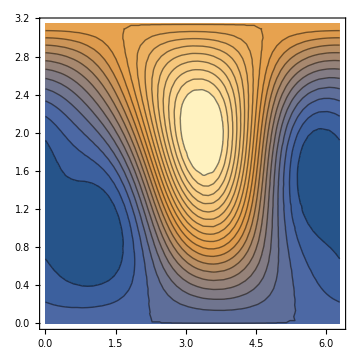
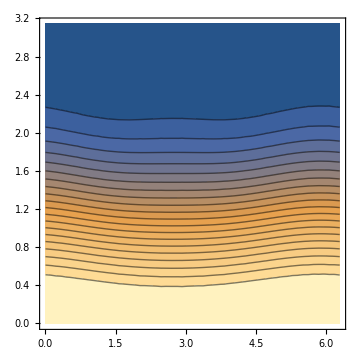
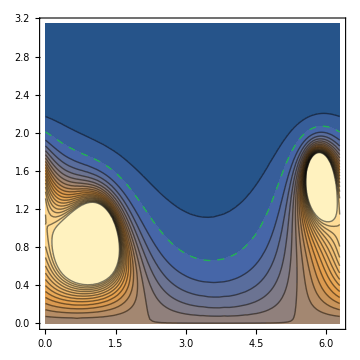

```mathematica
Ein=ParallelSum[With[{j1=u⟦1⟧,l1=u⟦2⟧,m1=u⟦3⟧,ω1=u⟦4⟧,Y1=u⟦5⟧,j2=v⟦1⟧,l2=v⟦2⟧,m2=v⟦3⟧,ω2=v⟦4⟧,Y2=v⟦5⟧},Y2*Y1 SpinWeightedSphericalHarmonicsY[1,l2,m2,θ,ϕ]*SpinWeightedSphericalHarmonicsY[1,l1,m1,θ,ϕ]],{u,InWavePackets},{v,InWavePackets}]//ComplexExpand//Chop;
Eout=ParallelSum[With[{j1=u⟦1⟧,l1=u⟦2⟧,m1=u⟦3⟧,ω1=u⟦4⟧,Z1=u⟦5⟧,j2=v⟦1⟧,l2=v⟦2⟧,m2=v⟦3⟧,ω2=v⟦4⟧,Z2=v⟦5⟧},Z2*Z1 SpinWeightedSphericalHarmonicsY[-1,l2,m2,θ,ϕ]*SpinWeightedSphericalHarmonicsY[-1,l1,m1,θ,ϕ]],{u,OutWavePackets},{v,OutWavePackets}]//ComplexExpand//Chop;
plots=ContourPlot[#,{ϕ,0,2Pi},{θ,0,Pi},ImageSize->Medium,ColorFunction->Automatic,Contours->20,ClippingStyle->Automatic,PlotRangePadding->Automatic]&/@{Ein,Eout,Eout/Ein-1};
plots/.Tooltip[x_,y_?PossibleZeroQ]:>Tooltip[x/.{l_Line->Sequence[Dashed,Thick,Green,l]},y]
```